## Naming Functions

## Delta N alpha

### Variables

```mathematica
M=10;
itNum=5000;
seed=1000;
divLst={80,16,16};
div=divLst⟦1⟧;
xLst=Table[it/div,{it,0,div}];
divLstStr=StringReplace[ToString[divLst],{"{"->"[","}"->"]"}];
attrLst={"N","param_divide","instanceNum","seed","alpha"};
fNameMod="alphaTest";
fNameMain="deltaN_distill";
alpha=0;
m=4;
```

### Labels

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"\\chi","\\langle \\left( \\Delta S_n \\right)^2 \\rangle"}
```

{-Graphics-,-Graphics-}

```mathematica
legDesc=MaTeX[#,Magnification->labMag]&/@{"\\alpha = \;\;\;\;\;\;"};
```

```mathematica
legDesc
```

{-Graphics-}

```mathematica
fName=fNameFun[fNameMain,{"N","param_divide","instanceNum","seed","alpha"},{M,divLst,itNum,seed,alpha},fNameMod,jldType]
```

deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_100_seed_1000_alpha_0_alphaTest.jld

```mathematica
ToString[NumberForm[1.0,{1,1}]]
```

1.0

```mathematica
alphaLst2=Table[0.2it,{it,0,5}]
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
alphaLst=Table[0.1it,{it,0,10}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

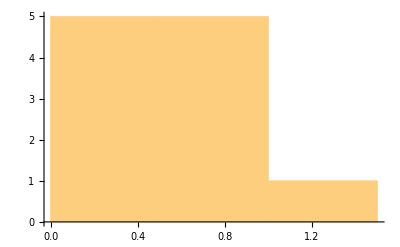

```mathematica
Histogram[alphaLst]
```

```mathematica
attrLst={"N","param_divide","instanceNum","seed","alpha"};
```

```mathematica
pltLst=ConstantArray[0,Length[alphaLst]];
```

```mathematica
pltLst
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
NumberForm[alpha,{1,1}]
```

1.0

```mathematica
Length[alphaLst]
```

11

```mathematica
itNum
```

5000

```mathematica
IntegerQ[alphaLst⟦1⟧]
```

False

### Plotting

```mathematica
alphaLst2=Table[0.2it,{it,0,5}];
alphaLstLeg=1-alphaLst2;
alphaLstLeg⟦1⟧=1;alphaLstLeg⟦-1⟧=0;
legLst=MaTeX[ToString[#],Magnification->labMag]&/@alphaLstLeg;
```

```mathematica
legLst
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[0;it,{it,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
fName
```

deltaN_distill_dim_10_N_[80, 16, 16]_param_divide_100_instanceNum_1000_seed_1.0_alphaTest.npy

```mathematica
datLst=Table[alpha=alphaLst2⟦ia⟧;
valLst={M,divLst,itNum,seed,NumberForm[alpha,{1,1}]};
If[ia<=1,
cutId=4;fModIa="";fModIa=fNameMod;fMainIa="deltaN_distill",
cutId=5;fModIa=fNameMod;fMainIa=fNameMain];
fName=fNameFun[fMainIa,attrLst⟦1;;cutId⟧,valLst⟦1;;cutId⟧,fModIa,npyType];
deltaNlst=readPython[fName];
yy={deltaNlst⟦m,-1⟧}~Join~deltaNlst⟦m⟧;
yy=(yy+Reverse[yy])/2;
{xLst,yy}ᵀ
,{ia,1,Length[alphaLst2]}];
```

```mathematica
colorLst={Black}~Join~(ColorData[112][#]&/@Table[ii,{ii,1,Length[alphaLst2]-1}])
```

{GrayLevel[0],RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831]}

```mathematica
,PlotLegends->LineLegend[legLst,LegendLabel->Placed[legDesc⟦1⟧,{{10,-2},Top}],Spacings->0.3]
```

```mathematica
figW
```

311.811

```mathematica
5cm
```

141.732

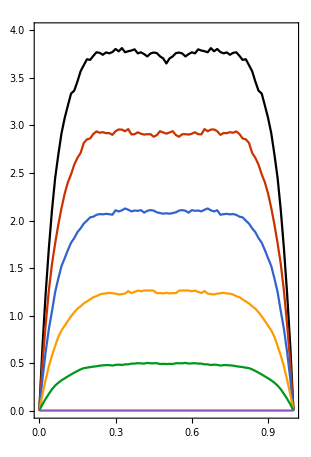

```mathematica
ListLinePlot[datLst,PlotStyle->colorLst,BaseStyle->texStyle,Frame->True,PlotRangePadding->{None,{0.01,None}},AspectRatio->(figH+4cm)/(figW-100),ImagePadding->imgPad,ImageSize->{figW,figH+4cm},PlotRange->{{0,1},{0,4}},Method->{"FrameInFront"->False},FrameLabel->xyLabs]
```

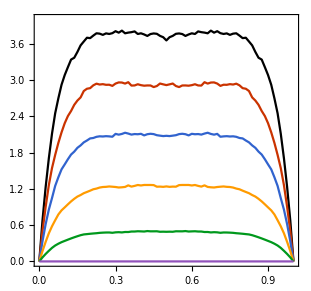

```mathematica
ListLinePlot[datLst,PlotStyle->colorLst,BaseStyle->texStyle,Frame->True,PlotRangePadding->{None,{0.01,None}},AspectRatio->figH/(figW-imgPad⟦1,2⟧),ImagePadding->imgPad,ImageSize->{figW,figH},PlotRange->{{0,1},{0,4}},Method->{"FrameInFront"->False},FrameLabel->xyLabs]
```

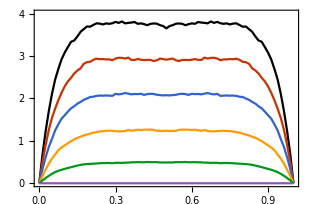

```mathematica
capLoc={0.07,0.9};
dNplt=Show[ListLinePlot[datLst,PlotStyle->colorLst,BaseStyle->texStyle,Frame->True,ImagePadding->imgPad,AspectRatio->aspRat,PlotRangePadding->{None,{0.01,None}},ImageSize->{figW,figH},PlotRange->{{0,1},{0,4}},Method->{"FrameInFront"->False},FrameLabel->xyLabs],Graphics[Text[capTex⟦1⟧,Scaled[capLoc]]]]
```

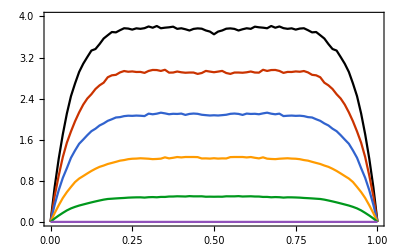

```mathematica
plt=Show[Legended[ListLinePlot[datLst,PlotStyle->colorLst,BaseStyle->texStyle,Frame->True,PlotRangePadding->{None,{0.01,None}},ImageSize->{Automatic,5cm},PlotRange->{{0,1},{0,4}},Method->{"FrameInFront"->False},FrameLabel->xyLabs],Placed[LineLegend[colorLst,legLst,LegendLabel->Placed[legDesc⟦1⟧,Left],LegendLayout->{"Row",1}],Below]]]
```

```mathematica
Export[exportDir<>"\\"<>"deltaN_alpha_0-1-0.2.eps",plt];
Export[exportDir<>"\\"<>"deltaN_alpha_0-1-0.2.jpg",plt];
```

```mathematica
pltLst=ConstantArray[0,Length[alphaLst2]];
For[ia=1,ia≤Length[alphaLst2],ia++,
alpha=alphaLst2⟦ia⟧;
valLst={M,divLst,itNum,seed,NumberForm[alpha,{1,1}]};
If[ia<=1,
cutId=4;fModIa="";fMainIa="deltaN_distill",
cutId=5;fModIa=fNameMod;fMainIa=fNameMain];
fName=fNameFun[fMainIa,attrLst⟦1;;cutId⟧,valLst⟦1;;cutId⟧,fModIa,npyType];
deltaNlst=readPython[fName];
yy={deltaNlst⟦m,-1⟧}~Join~deltaNlst⟦m⟧;
pltLst⟦ia⟧=ListLinePlot[{xLst,yy}ᵀ,BaseStyle->texStyle,(*PlotLegends->Placed[LineLegend[{legLst⟦ia⟧}],{{1,0.9-0.1ia},Right}],*)PlotStyle->{ColorData[97,ia],If[ia==Length[alphaLst2],4dataThick,2dataThick]},Method->{"FrameInFront"->False}];
]
```

```mathematica
Dimensions[pltLst]
```

{81}

```mathematica
pltLst
```

{}

```mathematica
pltLst⟦1⟧=1
```

Set::partw: Part 1 of {} does not exist.

1

```mathematica
legLst⟦ia⟧
```

-Graphics-

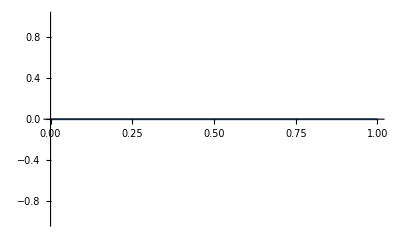

```mathematica
ListLinePlot[{xLst,yy}ᵀ,BaseStyle->texStyle,PlotLegends->"asdf"]
```

```mathematica
LineLegend[{Red},{legLst⟦ia⟧}]
```

```mathematica
Placed[LineLegend[legLst⟦ia⟧],{{1.2,0.8-0.1ia},Right}]
```

Placed[LineLegend[-Graphics-],{{1.2,0.2},Right}]

```mathematica
ia=6;
ListLinePlot[{xLst,yy}ᵀ,BaseStyle->texStyle,PlotStyle->{ColorData[97,ia],If[ia==Length[alphaLst2],5dataThick,dataThick]},PlotRange->Full,PlotLegends->Placed[LineLegend[{legLst⟦ia⟧}],{{1.2,0.8-0.1ia},Right}],Method->{"FrameInFront"->False}]
```

-Graphics-

```mathematica
Show[pltLst⟦1⟧]
```

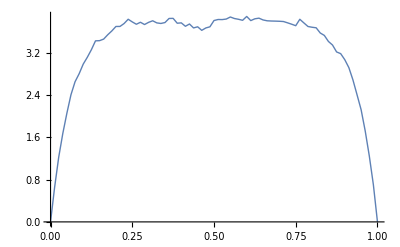

```mathematica
legDesc⟦1⟧
```

MaTeX[\alpha =,Magnification]

```mathematica
Graphics[Text[legDesc,Scaled[{1.1,0.9}]]]
```

-Graphics-

```mathematica
Show[pltLst~Join~{Graphics[Text[legDesc,Scaled[{1.1,0.9}]]]}]
```

-Graphics-

```mathematica
pltAll=Show[pltLst]
```

-Graphics-

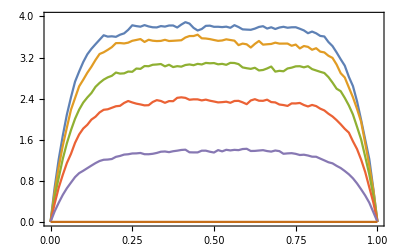

```mathematica
pltAll=Show[pltLst~Join~{Graphics[Text[legDesc⟦1⟧,Scaled[{1.1,0.9}]]]},BaseStyle->texStyle,Frame->True,PlotLegends->Placed[LineLegend[legLst],{{1,0.5},Right}],ImageSize->{Automatic,8cm},PlotRange->{{0,1},{0,4}},Method->{"FrameInFront"->False},FrameLabel->xyLabs,PlotRangeClipping->False]
```

```mathematica
Graphics[{Inset[pltAll,{0,0},{0,0},{.6,.6}],Text[legDesc⟦1⟧,Scaled[{1.1,0.9}]]},BaseStyle->texStyle,Frame->True,ImageSize->{10cm,8cm},PlotRangePadding->{None,{0.01,0}},PlotRange->{{0,1},{0,4}},Method->{"FrameInFront"->False},FrameLabel->xyLabs]
```

-Graphics-

```mathematica
fName=fNameFun[fNameMain,attrLst⟦1;;cutId⟧,valLst⟦1;;cutId⟧,fNameMod,npyType];
```

```mathematica
fName
```

deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000_alpha_1.0_alphaTest.npy

```mathematica
m
```

4

```mathematica
Dimensions[deltaNlst]
```

{9,80}

```mathematica
deltaNlst⟦m,-1⟧
```

0.0002

```mathematica
yy={deltaNlst⟦m,-1⟧}~Join~deltaNlst⟦m⟧;
```

```mathematica
Dimensions[yy]
```

{81}

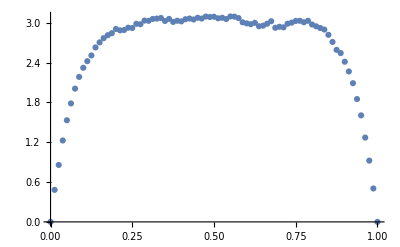

```mathematica
ListPlot[{xLst,yy}ᵀ]
```

```mathematica
deltaNlst=readPython[fName];
```

```mathematica
Dimensions[deltaNlst⟦4⟧]
```

{80}

```mathematica
plt=ListPlot[{xLst,deltaNlst⟦4⟧}ᵀ];
```

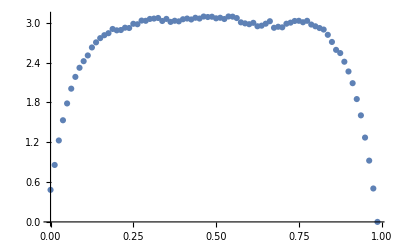

```mathematica
Show[plt,PlotRange->All]
```

```mathematica
Dimensions[deltaNlst⟦1⟧]
```

{}

```mathematica
fName=fNameMain~Join~"_N_"~Join~ToString[M]~Join~"_param_divide_"~Join~divLstStr~Join~"_instanceNum_"~Join~ToString[itNum]"_seed_"~Join~
```

```mathematica
StringReplace[ToString[divLst],{"{"->"[","}"->"]"}]
```

[80, 16, 16]

```mathematica
ArrayQ[10]
```

False

## Single shot plot

```mathematica
alpha=0;
valLst={M,divLst,itNum,seed,NumberForm[alpha,{1,1}]}
cutId=4;fModIa=fNameMod;fMainIa="deltaN_distill";
fName=fNameFun[fMainIa,attrLst⟦1;;cutId⟧,valLst⟦1;;cutId⟧,fModIa,npyType];
deltaNlst=readPython[fName];
yy={deltaNlst⟦m,-1⟧}~Join~deltaNlst⟦m⟧;
yy=(yy+Reverse[yy])/2;
```

{10,{80,16,16},100,1000,0}

Part::partw: Part 4 of Failure[PythonError,{MessageTemplate:>[Errno 2] No such file or directory: 'D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules\\\\deltaN_distill_N_10_param_divide_[80, 16, 16]_instanceNum_100_seed_1000.npy',MessageParameters:><||>,FailureCode:>FileNotFoundError,Traceback:>}] does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

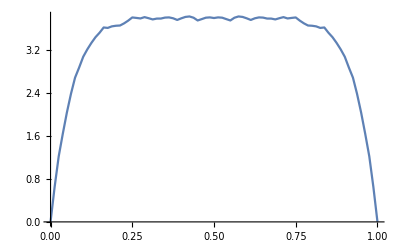

```mathematica
ListLinePlot[{xCoords,yy}ᵀ]
```